```mathematica
(* Filename: Errors_By_w2_SS_tuck_A1_2A1_sym_DN
*)
(* Ver. 0 (28-Aug-2025) *)
(*
This file is a program code in Mathematica to get a plot in Fig. 2.
*)
```

```mathematica
nn=127;
```

```mathematica
(***** In the following line, you need to set a path 
to the folder "For_figs_1_2". *****)
(*
datadir= "D:/.../For_figs_1_2/";
*)
```

```mathematica
mydirB4 = StringJoin[datadir,"/By_w2_SS_tuck_A1_2A1_sym_DN/dt=1_4/Se16_Tr1000_B256"];
(***)
mydirB8 = StringJoin[datadir,"/By_w2_SS_tuck_A1_2A1_sym_DN/dt=1_8/Se16_Tr1000_B256"];
(***)
mydirB16= StringJoin[datadir,"/By_w2_SS_tuck_A1_2A1_sym_DN/dt=1_16/Se16_Tr1000_B256"];
(***)
mydirB32 = StringJoin[datadir,"/By_w2_SS_tuck_A1_2A1_sym_DN/dt=1_32/Se16_Tr1000_B256"];
(***)
mydirB64 = StringJoin[datadir,"/By_w2_SS_tuck_A1_2A1_sym_DN/dt=1_64/Se16_Tr1000_B256"];
(***)
mydirA14 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_128/St14_Se16_Tr1000_B256"];
```

```mathematica
fdim=2;
numSetForPrecise=16;
```

```mathematica
numSetForData=16;
```

```mathematica
(* For precise solutions *)
dataMomA14ForEachY=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomA14ForEachY[[ii]]=Table[{},{ii,1,nn}];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirA14<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA14ForEachY[[ii]][[kk]]=locTmp[[kk]];
];
For[iiset = 2,iiset≤numSetForPrecise,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirA14<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA14ForEachY[[ii]][[kk]]+=locTmp[[kk]];
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomA14ForEachY[[ii]][[kk]]/=numSetForPrecise;

];
];(* End of for ii *)
```

```mathematica
dataMomB4ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomB4ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomB4ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomB4ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomB4ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirB4<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomB4ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirB4<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomB4ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomB4ForEachYAllSet[[ii]][[kk]]=dataMomB4ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomB4ForEachYAllSet[[ii]][[kk]]+=dataMomB4ForEachYEachSet[[ii,kk,iiset]];
];
dataMomB4ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomB8ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomB8ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomB8ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomB8ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomB8ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirB8<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomB8ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirB8<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomB8ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomB8ForEachYAllSet[[ii]][[kk]]=dataMomB8ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomB8ForEachYAllSet[[ii]][[kk]]+=dataMomB8ForEachYEachSet[[ii,kk,iiset]];
];
dataMomB8ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomB16ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomB16ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomB16ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomB16ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomB16ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirB16<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomB16ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirB16<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomB16ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomB16ForEachYAllSet[[ii]][[kk]]=dataMomB16ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomB16ForEachYAllSet[[ii]][[kk]]+=dataMomB16ForEachYEachSet[[ii,kk,iiset]];
];
dataMomB16ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomB32ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomB32ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomB32ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomB32ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomB32ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirB32<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomB32ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirB32<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomB32ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomB32ForEachYAllSet[[ii]][[kk]]=dataMomB32ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomB32ForEachYAllSet[[ii]][[kk]]+=dataMomB32ForEachYEachSet[[ii,kk,iiset]];
];
dataMomB32ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomB64ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomB64ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomB64ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomB64ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomB64ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirB64<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomB64ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirB64<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomB64ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomB64ForEachYAllSet[[ii]][[kk]]=dataMomB64ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomB64ForEachYAllSet[[ii]][[kk]]+=dataMomB64ForEachYEachSet[[ii,kk,iiset]];
];
dataMomB64ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
```

```mathematica
preciseMomForEachY=dataMomA14ForEachY;
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomB4=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomB4ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomB4[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomB8=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomB8ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomB8[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomB16=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomB16ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomB16[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomB32=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomB32ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomB32[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomB64=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomB64ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomB64[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
```

```mathematica
difflistMomB=Table[{},{ii,1,fdim}];
tmpMini=Table[{},{ii,1,5}];
For[ii=1, ii≤fdim, ii++,
tmpMini[[1]]={Log[2,1/4],Log[2,errorMomB4[[ii]]]};
tmpMini[[2]]={Log[2,1/8],Log[2,errorMomB8[[ii]]]};
tmpMini[[3]]={Log[2,1/16],Log[2,errorMomB16[[ii]]]};
tmpMini[[4]]={Log[2,1/32],Log[2,errorMomB32[[ii]]]};
tmpMini[[5]]={Log[2,1/64],Log[2,errorMomB64[[ii]]]};
difflistMomB[[ii]]=Table[tmpMini[[ii]],{ii,1,5}];
];
```

```mathematica
plotlistMomB=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotlistMomB[[ii]]=ListPlot[difflistMomB[[ii]],Joined->True,PlotStyle->Dashed(*,PlotStyle->Dashing[{0.075,0.05}]*)(*,PlotStyle->PointSize[0.02]*)];
];
```

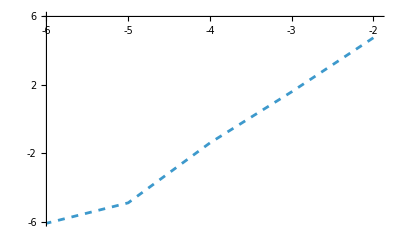

```mathematica
ll=0.015;
ii=1;
Show[plotlistMomB[[ii]],PlotRange->{{-6+0.05,-2+0.05},{-6,6}},AxesOrigin->{-6,6},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,2,6}],Table[{-2ii,ToString[-2ii],ll},{ii,-3,6}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```

```mathematica
numSubSetForData=8;(* 1, 2, 4, 8, 16 *)
numMiniSet=numSetForData/numSubSetForData;
(***)
dataMomB4ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomB4ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomB4ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
(*
If[(1==ii)&&(2>=kk),
Print["(ii=",ii,", kk=",kk,"); ","tmpSt=",tmpSt,", tmpEnd=",tmpEnd];
];
*)
dataMomB4ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomB4ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomB4ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomB4ForEachYEachSet[[ii,kk,iiset]];
];
dataMomB4ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomB8ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomB8ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomB8ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomB8ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomB8ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomB8ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomB8ForEachYEachSet[[ii,kk,iiset]];
];
dataMomB8ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomB16ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomB16ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomB16ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomB16ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomB16ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomB16ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomB16ForEachYEachSet[[ii,kk,iiset]];
];
dataMomB16ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomB32ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomB32ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomB32ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomB32ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomB32ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomB32ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomB32ForEachYEachSet[[ii,kk,iiset]];
];
dataMomB32ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomB64ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomB64ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomB64ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomB64ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomB64ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomB64ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomB64ForEachYEachSet[[ii,kk,iiset]];
];
dataMomB64ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
```

```mathematica
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomB4SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomB4SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomB4ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomB4ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomB4SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomB8SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomB8SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomB8ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomB8ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomB8SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomB16SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomB16SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomB16ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomB16ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomB16SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomB32SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomB32SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomB32ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomB32ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomB32SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomB64SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomB64SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomB64ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomB64ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomB64SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
```

```mathematica
errorMomB4Ave=Table[{},{ii,1,fdim}];
errorMomB4Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomB4SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomB4Ave[[ii]]=Mean[tmpErrorList];
errorMomB4Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomB4Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomB8Ave=Table[{},{ii,1,fdim}];
errorMomB8Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomB8SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomB8Ave[[ii]]=Mean[tmpErrorList];
errorMomB8Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomB8Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomB16Ave=Table[{},{ii,1,fdim}];
errorMomB16Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomB16SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomB16Ave[[ii]]=Mean[tmpErrorList];
errorMomB16Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomB16Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomB32Ave=Table[{},{ii,1,fdim}];
errorMomB32Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomB32SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomB32Ave[[ii]]=Mean[tmpErrorList];
errorMomB32Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomB32Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomB64Ave=Table[{},{ii,1,fdim}];
errorMomB64Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomB64SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomB64Ave[[ii]]=Mean[tmpErrorList];
errorMomB64Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomB64Ave[[ii]])^2]/numSubSetForData];
];
```

```mathematica
difflistMomBForAve=Table[{},{ii,1,fdim}];
tmpMini=Table[{},{ii,1,5}];
For[ii=1, ii≤fdim, ii++,
tmpMini[[1]]={Log[2,1/4],Log[2,errorMomB4Ave[[ii]]]};
tmpMini[[2]]={Log[2,1/8],Log[2,errorMomB8Ave[[ii]]]};
tmpMini[[3]]={Log[2,1/16],Log[2,errorMomB16Ave[[ii]]]};
tmpMini[[4]]={Log[2,1/32],Log[2,errorMomB32Ave[[ii]]]};
tmpMini[[5]]={Log[2,1/64],Log[2,errorMomB64Ave[[ii]]]};
difflistMomBForAve[[ii]]=Table[tmpMini[[ii]],{ii,1,5}];
];
```

```mathematica
plotlistMomBForAve=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotlistMomBForAve[[ii]]=ListPlot[difflistMomBForAve[[ii]],Joined->True,PlotStyle->Dashed(*,PlotStyle->Dashing[{0.075,0.05}]*)(*,PlotStyle->PointSize[0.02]*)];
];
```

```mathematica
plotMiniBarB4ForMom=Table[{},{ii,1,fdim}];
plotMiniBarB8ForMom=Table[{},{ii,1,fdim}];
plotMiniBarB16ForMom=Table[{},{ii,1,fdim}];
plotMiniBarB32ForMom=Table[{},{ii,1,fdim}];
plotMiniBarB64ForMom=Table[{},{ii,1,fdim}];
(***)
For[ii=1, ii≤fdim, ii++,
tmpStep=1/4;
plotMiniBarB4ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomB4Ave[[ii]]+errorMomB4Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomB4Ave[[ii]]-errorMomB4Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarB8ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomB8Ave[[ii]]+errorMomB8Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomB8Ave[[ii]]-errorMomB8Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarB16ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomB16Ave[[ii]]+errorMomB16Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomB16Ave[[ii]]-errorMomB16Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarB32ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomB32Ave[[ii]]+errorMomB32Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomB32Ave[[ii]]-errorMomB32Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarB64ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomB64Ave[[ii]]+errorMomB64Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomB64Ave[[ii]]-errorMomB64Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
];
```

```mathematica
tmpUpperListB=Table[{},{ii,1,fdim}];
tmpLowerListB=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpUpperListB[[ii]]={{Log[2,1/4],Log[2,errorMomB4Ave[[ii]]+errorMomB4Std[[ii]]]},{Log[2,1/8],Log[2,errorMomB8Ave[[ii]]+errorMomB8Std[[ii]]]},{Log[2,1/16],Log[2,errorMomB16Ave[[ii]]+errorMomB16Std[[ii]]]},{Log[2,1/32],Log[2,errorMomB32Ave[[ii]]+errorMomB32Std[[ii]]]},{Log[2,1/64],Log[2,errorMomB64Ave[[ii]]+errorMomB64Std[[ii]]]}};
tmpLowerListB[[ii]]={{Log[2,1/4],Log[2,errorMomB4Ave[[ii]]-errorMomB4Std[[ii]]]},{Log[2,1/8],Log[2,errorMomB8Ave[[ii]]-errorMomB8Std[[ii]]]},{Log[2,1/16],Log[2,errorMomB16Ave[[ii]]-errorMomB16Std[[ii]]]},{Log[2,1/32],Log[2,errorMomB32Ave[[ii]]-errorMomB32Std[[ii]]]},{Log[2,1/64],Log[2,errorMomB64Ave[[ii]]-errorMomB64Std[[ii]]]}};
];
```

```mathematica
plotMarkerListBForMom=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotMarkerListBForMom[[ii]]=ListPlot[{tmpUpperListB[[ii]],tmpLowerListB[[ii]]},PlotMarkers->{"",""}(*,PlotMarkers->{"",""}*)];
];
```

numSubSetForData=8

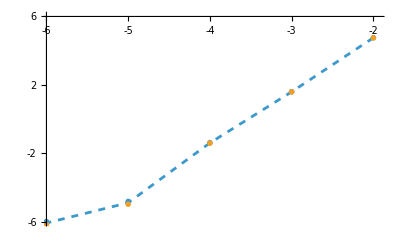

```mathematica
ll=0.03;
Print["numSubSetForData=",numSubSetForData];
ii=1;
Show[plotlistMomBForAve[[ii]],plotMarkerListBForMom[[ii]],plotMiniBarB4ForMom[[ii]],plotMiniBarB8ForMom[[ii]],plotMiniBarB16ForMom[[ii]],plotMiniBarB32ForMom[[ii]],plotMiniBarB64ForMom[[ii]],PlotRange->{{-6+0.05,-2+0.05},{-6,6}},AxesOrigin->{-6,6},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,2,6}],Table[{-2ii,ToString[-2ii],ll},{ii,-3,6}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```